# Runge-Kutta Method with Pendulum System

We looked into the Euler-Forward method, given by truncating the Taylor Series of a function after the first order term.
y(t + h) = y(t) + h y’(t) + h^2/2 y’’(t) + 𝒪(h^3)
For, y’(t) = f(y), we get the update equation,

```mathematica
updateEF={f,h}↦y↦y+h f@@y;
```

Which we can use iteratively to numerically solve systems such as the single frictionless pendulum,

```mathematica
f=Function[{θ,θp},{
θp,-Sin[θ]
}];
```

Let’s plot the parameter space and a solution trajectory,

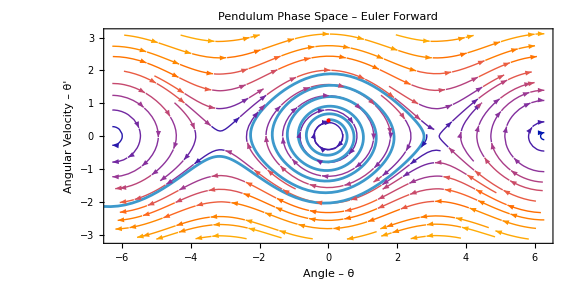

```mathematica
sp=StreamPlot[f[θ,θp],{θ,-2π,2π},{θp,-π,π},
AspectRatio->1/2,GridLines->{{-π,0,π},{0}},PlotRangePadding->None,ImageSize->Large,
FrameLabel->{"Angle – θ", "Angular Velocity – θ'"}
];
h=0.1;
initialState={0,0.5};
step=updateEF[f,h];
trajectory=NestList[step,initialState,500];
Show[sp,ListLinePlot[trajectory],ImageSize->Large,PlotLabel->"Pendulum Phase Space – Euler Forward",Epilog->{Red,PointSize[Large],Point[initialState]}]
```

This method predicts a growing energy even for a system with a conserved energy.
The Euler Forward method has a local error term of order h^2 and a global error h.
We can do better with the Runge–Kutta Method. It has the same signature as the Euler Forward method,
i.e. you provide it with a time derivative and a step size, and it will return a function that advances state-space coordinates in time.

```mathematica
updateRK4=Function[{f,h},Function[y1,
Module[{k1,k2,k3,k4,y2,y3,y4},
k1=Apply[f,y1];
y2=y1+h/2 k1;
k2=f@@y2;
y3=y1+h/2 k2;
k3=f@@y3;
y4=y1+h k3;
k4=f@@y4;
y1+h (k1+2k2+2k3+k4)/6
]
]];
```

Let’s re-run this trajectory with the RK4 method instead of Euler Forward,

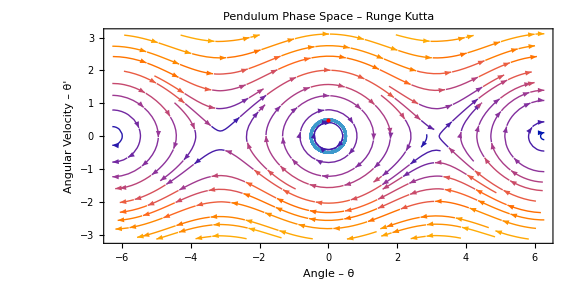

```mathematica
step=updateRK4[f,h];
trajectoryRK4=NestList[step,initialState,500];
Show[sp,ListLinePlot[trajectoryRK4],ImageSize->Large,PlotLabel->"Pendulum Phase Space – Runge Kutta",Epilog->{Red,PointSize[Large],Point[initialState]}]
```

We can use our solver to investigate different systems, such as a damping in the pendulum.
There are two models, one of an air resistance, which is damped proportional to velocity squared,

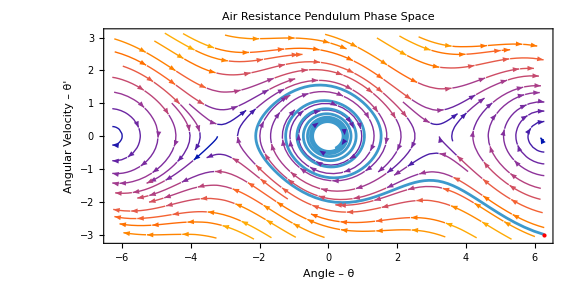

```mathematica
f={θ,θp}↦{
θp,
-Sin[θ]-0.1Sign[θp] θp^2
};
sp=StreamPlot[f[θ,θp],{θ,-2π,2π},{θp,-π,π},
AspectRatio->1/2,GridLines->{{-π,0,π},{0}},PlotRangePadding->None,ImageSize->Large,
FrameLabel->{"Angle – θ", "Angular Velocity – θ'"},PlotLabel->"Air Resistance Pendulum Phase Space"
];
h=0.1;
initialState={2π,-3};
step=updateRK4[f,h];
trajectoryRK4=NestList[step,initialState,500];
Show[sp,ListLinePlot[{trajectoryRK4},PlotRange->Full],ImageSize->Large,Epilog->{Red,PointSize[Large],Point[initialState]}]
```

The other model is of viscous damping which is linear in velocity,

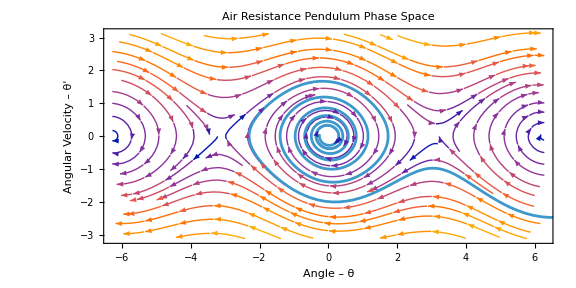

```mathematica
f={θ,θp}↦{
θp,
-Sin[θ]-0.1θp
};
sp=StreamPlot[f[θ,θp],{θ,-2π,2π},{θp,-π,π},
AspectRatio->1/2,GridLines->{{-π,0,π},{0}},PlotRangePadding->None,ImageSize->Large,
FrameLabel->{"Angle – θ", "Angular Velocity – θ'"},PlotLabel->"Air Resistance Pendulum Phase Space"
];
h=0.1;
initialState={4π,-3};
step=updateRK4[f,h];
trajectoryRK4=NestList[step,initialState,500];
Show[sp,ListLinePlot[{trajectoryRK4},PlotRange->Full],ImageSize->Large,Epilog->{Red,PointSize[Large],Point[initialState]}]
```